```mathematica
H1[p_]:=-p Log2[p]-(1-p) Log2[1-p];
H[a_, p_] := 1/(1-a) Log2[p^a + (1-p)^a];
H0[p_]:=Piecewise[{{H[0, p], 0 < p < 1}, {0, True}}];
μ[p_] := 2p-1;
```

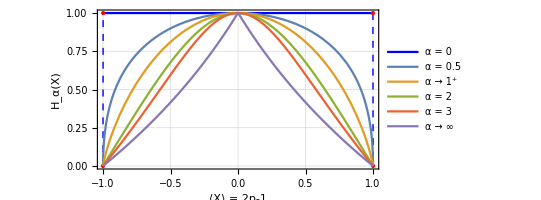

```mathematica
p1 = Show[
ParametricPlot[{μ[p],H0[p]}, {p,-0.001,1.001},PlotStyle->{Blue}, ExclusionsStyle->{{Blue,Dashed},Red}, PlotLegends->{"α = 0"}, PlotTheme->"Detailed", LabelStyle->Directive[FontSize->9]], 
ParametricPlot[{{μ[p],H[0.5,p]},
			    {μ[p],H1[p]},
			    {μ[p],H[2,p]},
			    {μ[p],H[3,p]},
			    {μ[p],H[500,p]}}, {p, -0, 1}, 
PlotTheme->"Detailed",PlotLegends->{"α = 0.5", "α → 1^+", "α = 2", "α = 3", "α → ∞"}, LabelStyle->Directive[FontSize->9]],
PlotRange->All,AxesOrigin->{0,0}, FrameLabel->{"⟨X⟩ = 2p-1", "H_α(X)"}, LabelStyle->Black
]
```

```mathematica
Export["plot.pdf",p1]
```

plot.pdf